# Convergence of Data Driven Coefficients

## for 2 D Tipping Cascade Data

## Function Initializations

## Making Windows

Starting from first data point.
Does not give the total number of windows possible.

```mathematica
MakeWindow[Data_,WL_,Overlap_,l_]:=
Module[{Lb,Hb,WO,TP},
TP=Length[Data];
WO=Floor[(1-Overlap)*WL];
Lb=1+((l-1)*WO);
Hb=(WL+((l-1)*WO));
(*{Lb,Hb}*)
Data[[Lb;;Hb]]
]
```

## Data Driven Reconstruction

### Core Function for Tipping Cascades

Here we are assuming all second order coefficients are zero and in third order coefficients all but the self interaction coefficient () are zero.
This gives an dataset (association) for each i (node name).
First element is R (not r but all zeroth order parts combined), and last element is  () term (a).
We have n+2 elements.

-Graphics-

```mathematica
TippingCoefsBasic[TimeSerieValues_,i_,dt_]:=(Module[{Y,Mat,Dim,TP,MatrixRowDef,MatrixRow,Coefs,CoefKeys},
Dim=Dimensions[Values[TimeSerieValues]];
TP=Dim[[2]];



CoefKeys=Join[{"\*SubscriptBox[R, "<>StringDelete[ToString[i]," "]<>"]"},Table["\*SubscriptBox[x, "<>StringDelete[ToString[j]," "]<>"]",{j,Keys[TimeSerieValues]}],{"\*SubscriptBox[x, "<>StringDelete[ToString[i]," "]<>"]"<>"^3"}];

MatrixRowDef=Join[{Table[1,TP]},Values[TimeSerieValues]];

MatrixRow=Join[MatrixRowDef,{TimeSerieValues[i]^3}];

Mat=Join[Table[MatrixRow.MatrixRowDef[[k]]/TP,{k,1,Dim[[1]]+1}],{MatrixRow.TimeSerieValues[i]^2/TP}];

Y=Join[Table[(TimeSerieValues[i][[2;;]]-TimeSerieValues[i][[;;-2]]).MatrixRowDef[[k]][[;;-2]]/(TP-1),{k,1,Dim[[1]]+1}],{(TimeSerieValues[i][[2;;]]-TimeSerieValues[i][[;;-2]]).TimeSerieValues[i][[;;-2]]^2/(TP-1)}];

Coefs=Association[Table[CoefKeys[[h]]->(LinearSolve[Mat,Y(*,Method->"Banded"*)]/dt)[[h]],{h,1,Dim[[1]]+2}]];

{Dataset[Coefs],Mat}
]
)
```

```mathematica
TippingCoefsBasic[TimeSerieValues_,i_,dt_]:=(Module[{Vars,Y,Mat,Dim,TP,MatrixRowDef,MatrixRow,Coefs,CoefKeys},
Dim=Dimensions[Values[TimeSerieValues]];
TP=Dim[[2]];

Vars=Table[Symbol["x"<>ToString[j]],{j,1,Dim[[1]]+2}];

CoefKeys=Join[{"\*SubscriptBox[R, "<>StringDelete[ToString[i]," "]<>"]"},Table["\*SubscriptBox[x, "<>StringDelete[ToString[j]," "]<>"]",{j,Keys[TimeSerieValues]}],{"\*SubscriptBox[x, "<>StringDelete[ToString[i]," "]<>"]"<>"^3"}];

MatrixRowDef=Join[{Table[1,TP]},Values[TimeSerieValues]];

MatrixRow=Join[MatrixRowDef,{TimeSerieValues[i]^3}];

Mat=Join[Table[MatrixRow.MatrixRowDef[[k]]/TP,{k,1,Dim[[1]]+1}],{MatrixRow.TimeSerieValues[i]^2/TP}];

Y=Join[Table[(TimeSerieValues[i][[2;;]]-TimeSerieValues[i][[;;-2]]).MatrixRowDef[[k]][[;;-2]]/(TP-1),{k,1,Dim[[1]]+1}],{(TimeSerieValues[i][[2;;]]-TimeSerieValues[i][[;;-2]]).TimeSerieValues[i][[;;-2]]^2/(TP-1)}];

Coefs=Association[Table[CoefKeys[[h]]->((Vars/.NSolve[Mat.Transpose[Vars]==Y,Vars,Method->"EndomorphismMatrix"])[[1]]/dt)[[h]],{h,1,Dim[[1]]+2}]];

{Dataset[Coefs],Mat,Y}
]
)
```

### Tipping Cascade Coefficients + Windowing

```mathematica
TippingCoefsWithWindow[TimeSerieValues_,i_,l_,dt_,WL_,Overlap_]:=(Module[{WindowTimeSerieValues,WindowTimeSerieValuesShuffle,Coefs,Errors,CoefsAfterError},

WindowTimeSerieValues=(MakeWindow[#,WL,Overlap,l]&)/@TimeSerieValues;

Coefs=TippingCoefsBasic[WindowTimeSerieValues,i,dt];

Coefs
]
)
```

### Moments

```mathematica
MomentCal[TimeSerieData_,Order_]:=(Module[{Vars,Dim},
Dim=Dimensions[Values[TimeSerieData]];

Vars=Table[Symbol["x"<>ToString[j]],{j,1,Dim[[1]]}];

Vars=Table[Symbol["x"<>ToString[j]],{j,1,Dim[[1]]}];
Expectation[Times@@Table[Vars,Order],Vars\[Distributed]Transpose[Values[TimeSerieData]]]
]
)
```

### General Drift Coefficients

DriftCoefsCalculator:

Description:
Computes drift coefficients of the specified polynomial orders from data

param “TimeSerieData”: All  time series.
type “TimeSerieData”: association with keys as names of time series and values as time  series (lists)(?) with same length.

param “Orders”: Specified orders to compute.
type “Orders”: list of integers.

param “nodes”: Nodes  to compute the drift for.
type “nodes”: list of key names.

param “dt”: Minimum time increment in time series.
type “dt”: precise(?) number.

```mathematica
DriftCoefsCalculator[TimeSerieData_,Orders_,nodes_,dt_]:=(Module[{Y,Mat,Dim,Coefs,CoefKeys,Vars,y},



Dim=Dimensions[Values[TimeSerieData]];

Vars=Table[Symbol["x"<>ToString[j]],{j,1,Dim[[1]]}];

CoefKeys=Join[{"α"},Flatten[Table[Flatten[{Outer@@Join[{StringJoin},Table[Table["\*SubscriptBox[x, "<>ToString[i]<>"]",{i,Keys[TimeSerieData]}],j]]}],{j,Select[Orders,#!=0&]}]]];

Mat=Expectation[TensorProduct[Flatten[Table[{TensorProduct@@Table[Vars,i]},{i,Orders}]],Flatten[Table[{TensorProduct@@Table[Vars,i]},{i,Orders}]]],Vars\[Distributed]Transpose[Values[TimeSerieData]]];


Y=Association[Table[node->Expectation[TensorProduct[y,Flatten[Table[Flatten[{TensorProduct@@Table[Vars,i]}],{i,Orders}]]],Join[{y},Vars]\[Distributed]Transpose[Join[{(TimeSerieData[node][[2;;]]-TimeSerieData[node][[;;-2]])},Values[TimeSerieData][[;;,;;-2]]]]],{node,nodes}]];

Coefs=Association[Table[node->Association[Table[CoefKeys[[h]]->(LinearSolve[Mat,Y[node]]/dt)[[h]],{h,1,Length[CoefKeys]}]],{node,nodes}]];



Dataset[Coefs]
]
)(*
Vars as local ?
runtime ?
diffusion ?
*)
```

## Generation of Data

This gives a temporal data for the tipping network.
It may be better to eliminate graph part and driver nodes and u.
We have the same problem of global variables x1, x2, ...
GenData format is in a way that data is n one dimensional timeseries.
We can have function for rm (but it does not show it as a time function in ItoProcess output ).
Data can be plotted with ListPlot, ListLinePlot and DateListPlot.
For now a, b, and x0 are set to be same for all nodes.

```mathematica
StochTippingDataGen[A_,SpecificGraph_,d_,TippedNodes_,rm_,DriverNodes_,UValue_,Noise_,dt_,InitVal_,FinalTime_]:=(Module[{n,B,r,eq,GenData,a=-1,b=1,x0=0},

n=Length[A];
r= Table[0&,n];

t=.;

r[[TippedNodes]]=rm;
B=A;
Do[B[[i,Complement[VertexOutComponent[SpecificGraph,i,1],{i}]]]=UValue,{i,DriverNodes}];



eq=Table[ⅆSymbol["x"<>ToString[i]][t]==(r[[i]][t]+b*(Symbol["x"<>ToString[i]][t]-x0)+a*(Symbol["x"<>ToString[i]][t]-x0)^3+d*Sum[Sqrt[-b/a]*Transpose[A][[i,j]],{j,1,n,1}]+d*Sum[Transpose[B][[i,j]]*(Symbol["x"<>ToString[j]][t]-x0),{j,1,n,1}])ⅆt+Noise*ⅆSymbol["w"<>ToString[i]][t],{i,1,n,1}];



GenData=RandomFunction[ItoProcess[eq,Table[Symbol["x"<>ToString[k]][t],{k,1,n}],{Table[Symbol["x"<>ToString[k]],{k,1,n}],InitVal},t,Table[Symbol["w"<>ToString[k]]\[Distributed]WienerProcess[],{k,1,n}]],{0.,FinalTime,dt},Method->"KloedenPlatenSchurz"];

GenData=TemporalData[Table[GenData["Values"][[;;,l]],{l,1,n}],{0,FinalTime}];

GenData
]
)
```

#### To not let error bars get negative

```mathematica
Clear[PosBar];
PosBar[y_]:=(Module[{x=y},
If[x[[2,1]]-x[[2,2]]<0,x[[2]]=Around[x[[2,1]],{x[[2,1]],x[[2,2]]}],x];
x
]
)
```

#### Latex Package

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
Needs["MaTeX`"]
```

```mathematica
ConfigureMaTeX[
"pdfLaTeX"->"C:\\texlive\\2017\\bin\\win32\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.02.1\\bin\\gswin64c.exe"
]
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\texlive\2017\bin\win32\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10.02.1\bin\gswin64c.exe}

```mathematica
MaTeX["
\\left[\\begin{array}{c}
\\left\\langle y_i(t, \\tau)\\right\\rangle \\\\
\\left\\langle y_i(t, \\tau) x_1\\right\\rangle \\\\
\\left\\langle y_i(t, \\tau) x_2\\right\\rangle \\\\
\\vdots \\\\
\\left\\langle y_i(t, \\tau) x_{\\mathcal{N}}\\right\\rangle \\\\
\\left\\langle y_i(t, \\tau) x_i^2\\right\\rangle
\\end{array}\\right]=\\left[\\begin{array}{cccccc}
1 & \\left\\langle x_1\\right\\rangle & \\left\\langle x_2\\right\\rangle & \\cdots & \\left\\langle x_{\\mathcal{N}}\\right\\rangle & \\left\\langle x_i^3\\right\\rangle \\\\
\\left\\langle x_1\\right\\rangle & \\left\\langle x_1^2\\right\\rangle & \\left\\langle x_1 x_2\\right\\rangle & \\cdots & \\left\\langle x_1 x_{\\mathcal{N}}\\right\\rangle & \\left\\langle x_1 x_i^3\\right\\rangle \\\\
\\left\\langle x_2\\right\\rangle & \\left\\langle x_1 x_2\\right\\rangle & \\left\\langle x_2^2\\right\\rangle & \\cdots & \\left\\langle x_2 x_{\\mathcal{N}}\\right\\rangle & \\left\\langle x_2 x_i^3\\right\\rangle \\\\
\\vdots & \\vdots & \\vdots & & \\vdots \\\\
\\left\\langle x_{\\mathcal{N}}\\right\\rangle & \\left\\langle x_1 x_{\\mathcal{N}}\\right\\rangle & \\left\\langle x_2 x_{\\mathcal{N}}\\right\\rangle & \\cdots & \\left\\langle x_{\\mathcal{N}}^2\\right\\rangle & \\left\\langle x_{\\mathcal{N}} x_i^3\\right\\rangle \\\\
\\left\\langle x_i^2\\right\\rangle & \\left\\langle x_1 x_i^2\\right\\rangle & \\left\\langle x_2 x_i^2\\right\\rangle & \\cdots & \\left\\langle x_{\\mathcal{N}} x_i^2\\right\\rangle & \\left\\langle x_i^5\\right\\rangle
\\end{array}\\right] \\times\\left[\\begin{array}{c}
R_i \\\\
A_{i, 1} \\\\
A_{i, 2} \\\\
\\vdots \\\\
b_i \\\\
\\vdots \\\\
a_i
\\end{array}\\right]
",FontSize->12]
```

-Graphics-

## Data

## Generate or Import

### Generate

#### Tipping Network

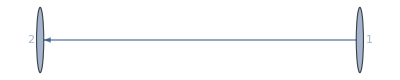

```mathematica
graph=Graph[{1->2},VertexLabels->Automatic,GraphLayout->"CircularEmbedding"]
```

#### SDE

```mathematica
MaTeX["\\begin{aligned}\\dot x_{i} &= r_i + b_{i}x_{i} + a_{i}x_{i}^3 + \\sum_{j=1}^{N} {d_{ij}x_{j}}\\end{aligned}",FontSize->15]
```

-Graphics-

For i=1  , and for other nodes 
If i!=j 
 if j is connected to i with a directed edge from j to i.

#### Data properties:

Diffusion is 
Initial values are 1.27, 1.24
All parameters are constant

```mathematica
A=AdjacencyMatrix[graph]//Normal;
```

```mathematica
SeedRandom[859];
Noise=√0.5;
dt=0.005;
GenData=StochTippingDataGen[A,graph,0.3,{1},0&,{1},1,Noise,dt,{-1,-1},50000]
```

TemporalData[…]

```mathematica
LocalObject["file:///C:/Users/alish/AppData/Roaming/Wolfram/Objects/e6eba485-bcf2-4b52-b7de-6a02cf2a1fbd"]
```

```mathematica
TimeSerieValues=Association[Table[ToString[i]->GenData["ValueList"][[i]],{i,1,2}]];
```

```mathematica
Mean[Transpose@GenData["ValueList"]]
```

{-0.00363516,0.662458}

```mathematica
GenData["ValueList"][[1,1;;4]]
```

{-1.,-1.02237,-1.04673,-1.05376}

```mathematica
GenData["ValueList"][[2,1;;4]]
```

{-1.,-1.00571,-0.912248,-0.882676}

```mathematica
Mean[{{1,2},{3,4}}]
```

{2,3}

#### Read data here.

```mathematica
(*Export[NotebookDirectory[]<>"2node_0_005_50000_sqrt0_5.csv",Transpose@(Values@TimeSerieValues)]*)
```

C:\Users\alish\Desktop\stability paper\2node_0_005_50000_sqrt0_5.csv

```mathematica
TimeSerieValuesImported=Transpose@Import[NotebookDirectory[]<>]
```

```mathematica
TimeSerieValues=Association[Table[ToString[i]->TimeSerieValuesImported[[i]],{i,1,2}]];
```

## Visualization

```mathematica
ListPlot[GenData["Paths"][[1]][[1;;1000000;;3]],
PlotRange->All,
ImageSize->Medium,
AspectRatio->1/8.5,
(*PlotLabel->Style["A",FontFamily->"Times",12],*)
Axes->False,
Frame->True,
FrameTicks->{{{-1,1},None},{Range[0,5000,1000],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["x_1",FontSize->12]},
PlotStyle->{Thickness[0.002],Black},
Joined->True]
```

-Graphics-

## Windowing and Coefficients

### Window sizes

Here we choose window sizes (N) and find out how many of each N we can have and what is Min(N).
Our ensemble size (MN) is equal or less than Min(N).

```mathematica
TimePoints=10000000;
Overlap=0/100;
```

```mathematica
WLs=Floor[PowerRange[500,500000,1.2]/100]*100
(*Logarithmic x axis is better because we can reach to large N and still show the convergence and Delta is still clear(y can not be logarthmic)*)
```

{400,600,700,800,1000,1200,1400,1700,2100,2500,3000,3700,4400,5300,6400,7700,9200,11000,13300,15900,19100,23000,27600,33100,39700,47600,57200,68600,82400,98900,118600,142400,170900,205000,246100,295300,354400,425200}

```mathematica
(*WLs=Join[Table[i,{i,500,40500,1000}]]*)
```

{500,1500,2500,3500,4500,5500,6500,7500,8500,9500,10500,11500,12500,13500,14500,15500,16500,17500,18500,19500,20500,21500,22500,23500,24500,25500,26500,27500,28500,29500,30500,31500,32500,33500,34500,35500,36500,37500,38500,39500,40500}

```mathematica
(*WLs=Join[Table[i,{i,75000,500000,50000}],{400000}]*)
```

This finds total number of windows with size N which we can have in the specified “TimePoints”.

```mathematica
WindowNumbers=Table[With[{TP=TimePoints,Overlap=Overlap,WL=i},Floor[(TP-(Overlap*WL))/((1-Overlap)*WL)]],{i,WLs}]
```

{25000,16666,14285,12500,10000,8333,7142,5882,4761,4000,3333,2702,2272,1886,1562,1298,1086,909,751,628,523,434,362,302,251,210,174,145,121,101,84,70,58,48,40,33,28,23}

```mathematica
WLsAndWindowNumbers=MapThread[List,{WLs,WindowNumbers}]
```

{{400,25000},{600,16666},{700,14285},{800,12500},{1000,10000},{1200,8333},{1400,7142},{1700,5882},{2100,4761},{2500,4000},{3000,3333},{3700,2702},{4400,2272},{5300,1886},{6400,1562},{7700,1298},{9200,1086},{11000,909},{13300,751},{15900,628},{19100,523},{23000,434},{27600,362},{33100,302},{39700,251},{47600,210},{57200,174},{68600,145},{82400,121},{98900,101},{118600,84},{142400,70},{170900,58},{205000,48},{246100,40},{295300,33},{354400,28},{425200,23}}

```mathematica
MN=Last[WindowNumbers]
```

23

```mathematica
MN=50;(*ensemble size*)
```

### Coefficients for each N

```mathematica
SeedRandom[369];
WLsAndWindowSample=MapThread[List,{WLs,Table[RandomSample[Range[1,WL],MN],{WL,WindowNumbers}]}];
```

```mathematica
MomentsAllWinSize=Table[Transpose@Table[MeanAround/@(Transpose@Table[MomentCal[(MakeWindow[#,WL[[1]],Overlap,l]&)/@TimeSerieValues,i],{l,WL[[2]]}]),{WL,WLsAndWindowSample}],{i,{2,4,6,8,10,12}}];
```

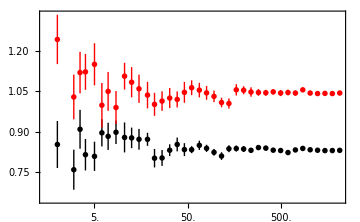

```mathematica
gx2=ListPlot[Table[MapThread[List,{WLs,MomentsAllWinSize[[1]][[i]]}],{i,1,2}],
Frame->True,(*FrameTicks->{{Automatic,None},{Automatic,None}},*)FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["<x^2>",FontSize->12]},
(*PlotLabel->Style["A",15,FontFamily->"Times"],*)
PlotRange->{Automatic,Automatic},
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
PlotStyle->{Black,Red},
ImagePadding->{{55, 10}, {Automatic, Automatic}},
ImageSize->Medium,
PlotLegends->Placed[Table[MaTeX[ToString[i],FontSize->10],{i,1,2}],{0.9,0.8}]]
```

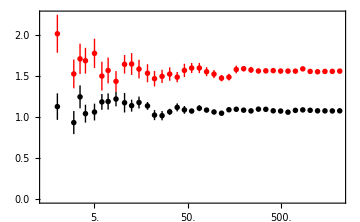

```mathematica
gx4=ListPlot[Table[MapThread[List,{WLs,MomentsAllWinSize[[2]][[i]]}],{i,1,2}],
Frame->True,(*FrameTicks->{{Automatic,None},{Automatic,None}},*)FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["<x^4>",FontSize->12]},
(*PlotLabel->Style["A",15,FontFamily->"Times"],*)
PlotRange->{Automatic,Automatic},
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
PlotStyle->{Black,Red},
ImagePadding->{{55, 10}, {Automatic, Automatic}},
ImageSize->Medium,
PlotLegends->Placed[Table[MaTeX[ToString[i],FontSize->10],{i,1,2}],{0.9,0.8}]]
```

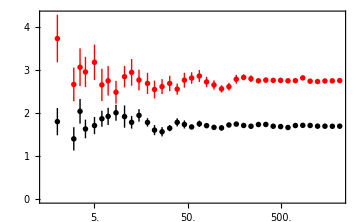

```mathematica
gx6=ListPlot[Table[MapThread[List,{WLs,MomentsAllWinSize[[3]][[i]]}],{i,1,2}],
Frame->True,(*FrameTicks->{{Automatic,None},{Automatic,None}},*)FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["<x^6>",FontSize->12]},
(*PlotLabel->Style["A",15,FontFamily->"Times"],*)
PlotRange->{Automatic,Automatic},
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
PlotStyle->{Black,Red},
ImagePadding->{{55, 10}, {Automatic, Automatic}},
ImageSize->Medium,
PlotLegends->Placed[Table[MaTeX[ToString[i],FontSize->10],{i,1,2}],{0.9,0.8}]]
```

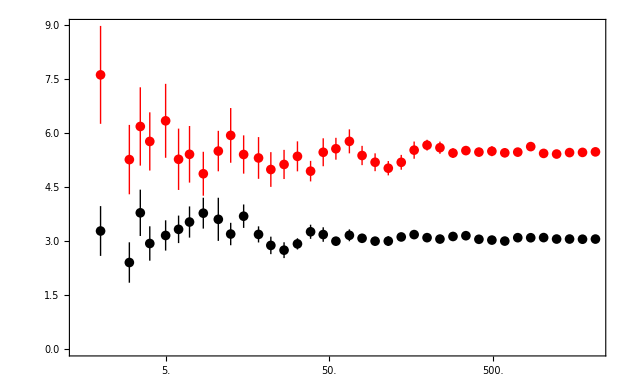

```mathematica
gx8=ListPlot[Table[MapThread[List,{WLs,MomentsAllWinSize[[4]][[i]]}],{i,1,2}],
Frame->True,(*FrameTicks->{{Automatic,None},{Automatic,None}},*)FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["<x^8>",FontSize->12]},
(*PlotLabel->Style["A",15,FontFamily->"Times"],*)
PlotRange->{Automatic,Automatic},
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
PlotStyle->{Black,Red},
ImagePadding->{{55, 10}, {Automatic, Automatic}},
ImageSize->Medium,
PlotLegends->Placed[Table[MaTeX[ToString[i],FontSize->10],{i,1,2}],{0.9,0.8}]]
```

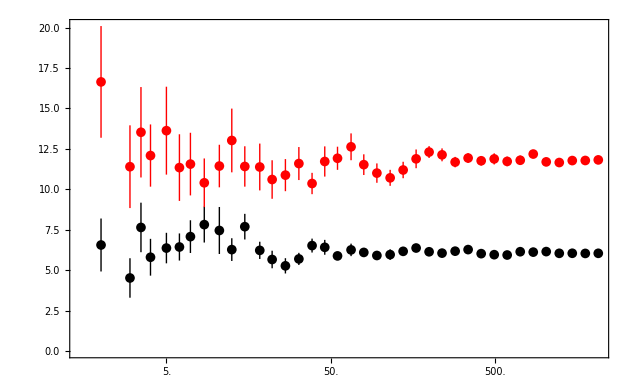

```mathematica
gx10=ListPlot[Table[MapThread[List,{WLs,MomentsAllWinSize[[5]][[i]]}],{i,1,2}],
Frame->True,(*FrameTicks->{{Automatic,None},{Automatic,None}},*)FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["<x^{10}>",FontSize->12]},
(*PlotLabel->Style["A",15,FontFamily->"Times"],*)
PlotRange->{Automatic,Automatic},
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
PlotStyle->{Black,Red},
ImagePadding->{{55, 10}, {Automatic, Automatic}},
ImageSize->Medium,
PlotLegends->Placed[Table[MaTeX[ToString[i],FontSize->10],{i,1,2}],{0.9,0.8}]]
```

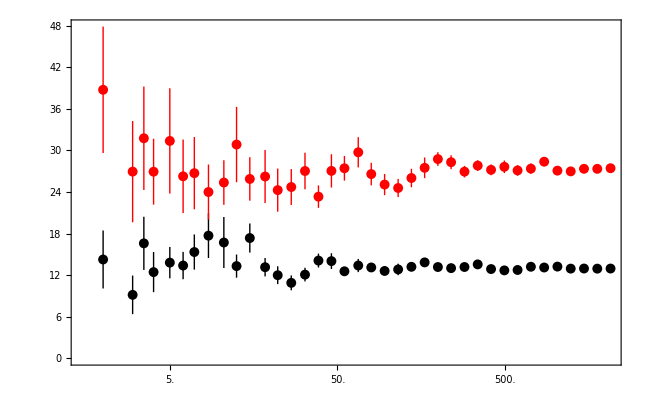

```mathematica
gx12=ListPlot[Table[MapThread[List,{WLs,MomentsAllWinSize[[6]][[i]]}],{i,1,2}],
Frame->True,(*FrameTicks->{{Automatic,None},{Automatic,None}},*)FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["<x^{12}>",FontSize->12]},
(*PlotLabel->Style["A",15,FontFamily->"Times"],*)
PlotRange->{Automatic,Automatic},
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
PlotStyle->{Black,Red},
ImagePadding->{{55, 10}, {Automatic, Automatic}},
ImageSize->Medium,
PlotLegends->Placed[Table[MaTeX[ToString[i],FontSize->10],{i,1,2}],{0.9,0.8}]]
```

```mathematica
XmCoeffsAllWinSize=Table[Table[Table[Values@Normal[TippingCoefsWithWindow[TimeSerieValues,ToString[m],l,dt,WL[[1]],Overlap]],{l,WL[[2]]}],{WL,WLsAndWindowSample}],{m,1,2}];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
TippingCoefsWithWindow[TimeSerieValues,ToString[1],23,dt,425200,Overlap]
```

{,{{1.,0.0526389,0.760814,0.0384551},{0.0526389,0.848509,0.239076,1.10261},{0.760814,0.239076,1.05531,0.262073},{0.848509,0.0384551,0.635061,0.0268376}}}

```mathematica
{{1.,0.0526388514054032,0.7608144225486715,0.038455116965255526},{0.0526388514054032,0.8485090037722312,0.23907637481475896,1.1026074777420012},{0.7608144225486715,0.23907637481475896,1.0553104576051986,0.2620726428345378},{0.8485090037722312,0.038455116965255526,0.6350613694991141,0.026837578860375418}}//MatrixForm
```

(1. | 0.0526389 | 0.760814 | 0.0384551
0.0526389 | 0.848509 | 0.239076 | 1.10261
0.760814 | 0.239076 | 1.05531 | 0.262073
0.848509 | 0.0384551 | 0.635061 | 0.0268376)

```mathematica
%//Det
```

0.000631475

## Convergence Plots for a, b, r and d

## Δa

```mathematica
gadata=Table[MapThread[List,{WLs,Abs@((MeanAround/@(XmCoeffsAllWinSize[[i]][[All,All,2+2]]))+1)}],{i,1,2}];
```

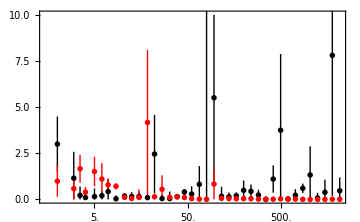

```mathematica
ga=ListPlot[Map[PosBar,gadata,{2}],Frame->True,(*FrameTicks->{{Automatic,None},{Automatic,None}},*)FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["|\\Delta a|",FontSize->12]},
(*PlotLabel->Style["A",15,FontFamily->"Times"],*)
PlotRange->{Automatic,{0,10}},
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
PlotStyle->{Black,Red},
ImagePadding->{{55, 10}, {Automatic, Automatic}},
ImageSize->Medium,
PlotLegends->Placed[Table[MaTeX[ToString[i],FontSize->10],{i,1,2}],{0.9,0.8}]]
```

```mathematica
Export[NotebookDirectory[]<>"2D_delta_a.pdf",ga]
```

C:\Users\alish\Desktop\stability paper\2D_delta_a.pdf

## Δb

```mathematica
MapThread[List,{WLs,Abs@((MeanAround/@(XmCoeffsAllWinSize[[1]][[All,All,2]]))-1)}]
```

{{500,5.72.5},{1500,1.01.1},{2500,1.10.8},{3500,0.70.9},{4500,1.60.8},{5500,0.500.27},{6500,1.120.34},{7500,0.850.27},{8500,0.910.29},{9500,0.90.4},{10500,0.50.4},{11500,0.600.30},{12500,0.380.19},{13500,0.650.31},{14500,0.500.35},{15500,0.370.22},{16500,0.200.17},{17500,0.490.25},{18500,0.890.29},{19500,0.300.14},{20500,0.650.15},{21500,0.360.29},{22500,0.440.23},{23500,0.460.25},{24500,0.080.12},{25500,0.190.13},{26500,0.610.22},{27500,0.420.14},{28500,0.030.13},{29500,0.570.20},{30500,0.370.28},{31500,0.550.12},{32500,0.220.16},{33500,0.230.12},{34500,0.260.16},{35500,0.090.15},{36500,0.490.14},{37500,0.140.10},{38500,0.060.11},{39500,0.100.12},{40500,0.090.18},{200000,0.070.04}}

```mathematica
gbdata=Table[MapThread[List,{WLs,Abs@((MeanAround/@(XmCoeffsAllWinSize[[i]][[All,All,i+1]]))-1)}],{i,1,2}];
```

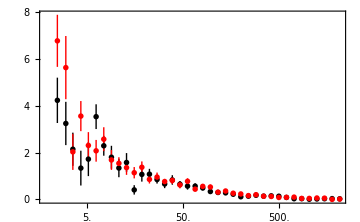

```mathematica
gb=ListPlot[Map[PosBar,gbdata,{2}],Frame->True,
(*FrameTicks->{{Automatic,None},{Automatic,None}},*)
FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["|\\Delta b|",FontSize->12]},
(*PlotLabel->Style["B",15,FontFamily->"Times"],*)
PlotRange->All,
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
PlotLegends->Placed[Table[MaTeX[ToString[i],FontSize->10],{i,1,2}],{0.9,0.8}],
ImageSize->Medium,
PlotStyle->{Black,Red},
ImagePadding->{{55, 10}, {Automatic, Automatic}}]
```

```mathematica
Export[NotebookDirectory[]<>"2D_delta_b.pdf",gb]
```

C:\Users\alish\Desktop\stability paper\2D_delta_b.pdf

## Δd

```mathematica
(*AllEdges=Flatten[Table[{i,j},{i,1,10},{j,Select[Range[1,10],#!=i&]}],1]*)
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,1},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,1},{3,2},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,1},{4,2},{4,3},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,1},{5,2},{5,3},{5,4},{5,6},{5,7},{5,8},{5,9},{5,10},{6,1},{6,2},{6,3},{6,4},{6,5},{6,7},{6,8},{6,9},{6,10},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,8},{7,9},{7,10},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,9},{8,10},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,10},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9}}

```mathematica
(*OnEdges=Select[AllEdges,A[[#[[1]],#[[2]]]]!=0&]*)
```

{{1,2},{1,4},{1,8},{2,3},{2,5},{3,9},{4,2},{4,3},{5,1},{5,3},{5,6},{5,7},{5,10},{7,8},{8,6},{8,9},{10,4}}

```mathematica
(*OffEdges=Select[AllEdges,A[[#[[1]],#[[2]]]]==0&]*)
```

{{1,3},{1,5},{1,6},{1,7},{1,9},{1,10},{2,1},{2,4},{2,6},{2,7},{2,8},{2,9},{2,10},{3,1},{3,2},{3,4},{3,5},{3,6},{3,7},{3,8},{3,10},{4,1},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,2},{5,4},{5,8},{5,9},{6,1},{6,2},{6,3},{6,4},{6,5},{6,7},{6,8},{6,9},{6,10},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,9},{7,10},{8,1},{8,2},{8,3},{8,4},{8,5},{8,7},{8,10},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,10},{10,1},{10,2},{10,3},{10,5},{10,6},{10,7},{10,8},{10,9}}

```mathematica
gcdata=Table[MapThread[List,{WLs,Abs@((MeanAround/@(XmCoeffsAllWinSize[[s[[1]]]][[All,All,1+s[[2]]]]))-0.3A[[s[[2]],s[[1]]]])}],{s,{{1,2},{2,1}}}];
```

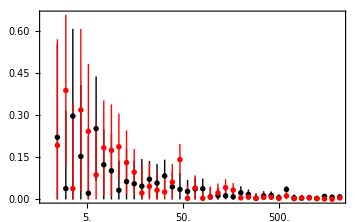

```mathematica
gc=ListPlot[Map[PosBar,gcdata,{2}],Frame->True,
(*FrameTicks->{{Automatic,None},{Automatic,None}},*)FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)(*{{500,0.5},{1000,1},{5000,5},{10^4,10},{5*10^4,50},{10^5,100}}*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["|\\Delta d|",FontSize->12]},(*PlotLabel->Style["C",15,FontFamily->"Times"],*)
PlotRange->All,
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
ImageSize->Medium,
PlotLegends->Placed[Table[MaTeX["d_{"<>ToString[s[[2]]]<>","<>ToString[s[[1]]]<>"}",FontSize->10],{s,{{1,2},{2,1}}}],{0.9,0.8}],
PlotStyle->{Black,Red},
ImagePadding->{{55, 10}, {Automatic, Automatic}}]
```

```mathematica
Export[NotebookDirectory[]<>"2D_delta_d.pdf",gc]
```

C:\Users\alish\Desktop\stability paper\2D_delta_d.pdf

## Δr

```mathematica
MapThread[List,{WLs,Abs@((MeanAround/@(X1CoeffsAllWinSize[[All,All,1]]))-0.79)}]
```

{{500,5.52.1},{1500,0.91.1},{2500,1.50.8},{3500,1.00.7},{4500,1.40.7},{5500,0.580.29},{6500,0.590.30},{7500,0.560.20},{8500,0.840.28},{9500,0.680.32},{10500,0.460.23},{11500,0.450.27},{12500,0.240.16},{13500,0.500.22},{14500,0.540.31},{15500,0.300.23},{16500,0.110.10},{17500,0.430.23},{18500,0.600.22},{19500,0.150.13},{20500,0.470.17},{21500,0.250.25},{22500,0.300.14},{23500,0.340.23},{24500,0.160.11},{25500,0.110.10},{26500,0.430.17},{27500,0.190.10},{28500,0.020.10},{29500,0.350.19},{30500,0.340.22},{31500,0.400.11},{32500,0.320.13},{33500,0.100.07},{34500,0.220.12},{35500,0.090.14},{36500,0.260.13},{37500,0.170.07},{38500,0.060.08},{39500,0.100.07},{40500,0.070.14},{200000,0.0310.028}}

```mathematica
gddata=Table[MapThread[List,{WLs,Abs@((MeanAround/@(XmCoeffsAllWinSize[[i]][[All,All,1]]))-If[i==1,0.79+0.3*Sum[A[[j,i]],{j,1,2}],0.3*Sum[A[[j,i]],{j,1,2}]])}],{i,1,2}];
```

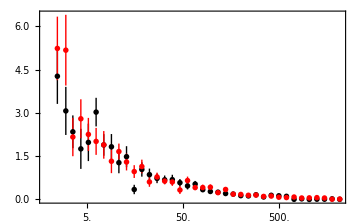

```mathematica
gd=ListPlot[Map[PosBar,gddata,{2}],Frame->True,(*FrameTicks->{{Automatic,None},{Automatic,None}},*)
FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["|\\Delta r|",FontSize->12]},(*PlotLabel->Style["D",15,FontFamily->"Times"],*)
PlotRange->All,
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
PlotLegends->Placed[Table[MaTeX[ToString[i],FontSize->10],{i,1,2}],{0.9,0.8}],
ImageSize->Medium,
PlotStyle->{Black,Red},
ImagePadding->{{55, 10}, {Automatic, Automatic}}]
```

```mathematica
Export[NotebookDirectory[]<>"2D_delta_r.pdf",gd]
```

C:\Users\alish\Desktop\stability paper\2D_delta_r.pdf

```mathematica
legend=PointLegend[{Black,Darker[Green]},{1,2},(*LegendMarkers->Graphics[{EdgeForm[None],Opacity[1],Disk[]}],*)LegendMarkerSize->10,LegendLayout->"Row",LegendFunction->(Framed[#,RoundingRadius->3,FrameStyle->LightGray]&),LegendMargins->1,LabelStyle->{12,FontFamily->"Times"}(*,LegendLabel->Placed[Style["no. fixed points",12],Below]*)]
```

```mathematica
gg=Legended[GraphicsColumn[{GraphicsRow[{ga,gb}],GraphicsRow[{gc,gd}]}],Placed[legend,Below]]
```

-Graphics-

## Results & Figures

Diffusion is 
Initial values are 
All parameters are constant



Overlap = 70/100
Data Point = 10^7

### Figure Draft

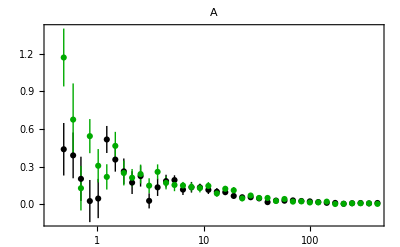

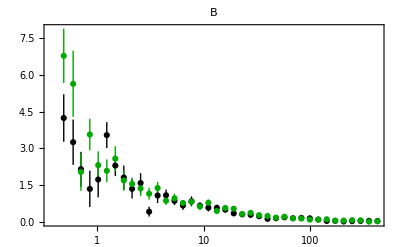

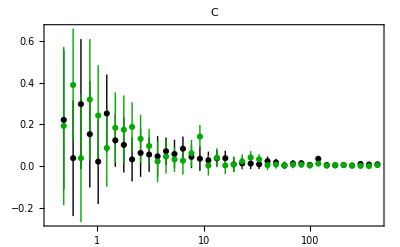

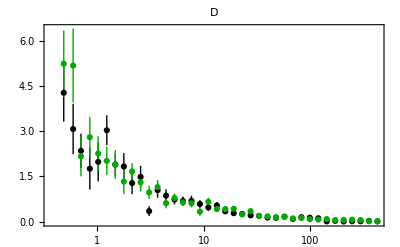

## Conclusion & Summary

We construct a long (10^7 data point) data for a unidirectional tipping system, and then we show that by increasing window size (N) all coefficients driven from data converge to the theoretical values by which data is constructed with. For every N we construct an ensemble of windows with 70% overlap. Ensembles are of the same size, 50. Each point on the figures is the average of the coefficient on the ensemble of size N. We see high accuracy for N>10^5.

## Figure Data Manipulation and Export

```mathematica
Do[Export[NotebookDirectory[]<>"2D_delta_a_"<>ToString[i]<>".txt",Map[Flatten,gadata/.Around->List,{2}][[i]],"Table","FieldSeparators"->Tab],{i,1,2}]
```

```mathematica
Do[Export[NotebookDirectory[]<>"2D_delta_b_"<>ToString[i]<>".txt",Map[Flatten,gbdata/.Around->List,{2}][[i]],"Table","FieldSeparators"->Tab],{i,1,2}]
```

```mathematica
Do[Export[NotebookDirectory[]<>"2D_delta_r_"<>ToString[i]<>".txt",Map[Flatten,gddata/.Around->List,{2}][[i]],"Table","FieldSeparators"->Tab],{i,1,2}]
```

```mathematica
Do[Export[NotebookDirectory[]<>"2D_delta_d_nonzero_"<>ToString[i]<>".txt",Map[Flatten,gcdata/.Around->List,{2}][[i]],"Table","FieldSeparators"->Tab],{i,1,2}]
```